```mathematica
$HistoryLength = 0
```

0

```mathematica
<<NonStandartImportExport`
```

```mathematica
file = 
FileNameJoin[{NotebookDirectory[],"NonStandartImportExportExample","segy_test_input.segy"}]
```

E:\Test Items\Wolfram Language\Mathematica\Projects\NonStandartImportExport\NonStandartImportExportExample\segy_test_input.segy

Import to the memory

```mathematica
AbsoluteTiming[data1 = NonStandartImport[file, "SGY"];]
```

{0.0652211,Null}

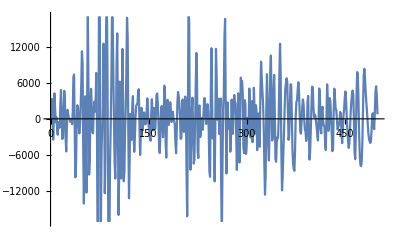

```mathematica
ListLinePlot[data1[[-1, -1, -1, 1]]]
```

Delayed import

```mathematica
AbsoluteTiming[data2 = NonStandartImport[file, "SGY", Loading -> "Delayed"];]
```

{0.0339317,Null}

```mathematica
data2[[-1, -1, -1, 1]]
```

SEGYUnloaded[{File→E:\Test Items\Wolfram Language\Mathematica\Projects\NonStandartImportExport\NonStandartImportExportExample\segy_test_input.segy,Start→3840,Bytes→2000,Function→Function[{NonStandartImportExport`Extensions`SEGY`Private`bytes$},FromNonStandartNumberFormat[NonStandartImportExport`Extensions`SEGY`Private`bytes$,NumberFormat/.{TimeInterval→1/250,TrackLength→500,NumberFormat→1}]]}]

```mathematica
ListLinePlot[NonStandartLoad[data2[[-1, -1, -1, 1]]]]
```

-Graphics-